```mathematica
(* PŘÍKLAD 1 *)
```

```mathematica
ClearAll["Global`*"]

Ib = 150*10^-6;
β = 80.; (* informace z katalogového listu *)
Rc = 220;
U2 = 10;
Ube = 0.7; (* informace z katalogového listu *)

Ic = β*Ib;
Print["Proud Ic = ", Ic, " A." ]
URc = Rc*Ic
Uce = U2-URc

(* ztrátový výkon *)
PRc = Ic*URc
(* PT = Ic*Uce *)
PT = Ic*Uce+Ib*Ube
```

Proud Ic = 0.012 A.

2.64

7.36

0.03168

0.08832

0.088425

```mathematica
(* PŘÍKLAD 2 *)
```

```mathematica
ClearAll["Global`*"]
U1 = 6;
U2 = 18;
Rb = 56*10^3;
Rc = 1.5*10^3;
β = 70;
Ube = 0.7;

URb = U1-Ube
Ib = URb/Rb
Ic = Ib*β
URc = Ic*Rc
Uce = U2-URc
(* ztrátový výkon *)
PRc = Ic*URc
PT = Uce*Ic+Ube*Ib
```

5.3

0.0000946429

0.006625

9.9375

8.0625

0.0658359

0.0534803

```mathematica
(* PŘÍKLAD 3 *)
```

```mathematica
ClearAll["Global`*"]
U1 = 5;
U2=12;
Rb = 100*10^3;
Rc = 3.3*10^3;
β = 110;
Ube = 0.7;
Uce = 0.2; (* tranzistor je v saturaci *)

URb = U1-Ube
Ib = URb/Rb

(* Ic =β*Ib -> tranzistor je v saturaci - toto nebude fungovat*)
(* URc = Rc*Ic  bacha *)
(* Uce = U2-URc problém *)
URc = U2-Uce
Ic = URc/Rc
(* ztrátový výkon *)
PRc = Ic*URc
PT = Ic*Uce+Ib*Ube
```

4.3

0.000043

11.8

0.00357576

0.0421939

0.000745252

```mathematica
(* PŘÍKLAD 4 *)
```

```mathematica
ClearAll["Global`*"]
U1=8.;
U2 = 12;
R1 = 150*10^3;
R2=220*10^3;
Rd = 470;
Uth = 2.5; (* prahové napětí - toto bude vždy zadáno - z katalogových listů *)
k = 2*10^-3; (* činitel K - toto bude vždy zadáno - z katalogových listů *)

(* vsuvka: Jak spočítat napětí na rezistoru R2 neboli Ugs *)
Idelic = U1/(R1+R2)
UR2 = Idelic*R2
(* konec vsuvky *)

Ugs = U1*R2/(R1+R2)
UR2==Ugs

Id = k*(Ugs-Uth)^2/2  (* vzoreček *)
URd = Id*Rd
Uds = U2-URd
(* ztrátové výkony *)
PRd = URd*Id
PT = Uds*Id
```

0.0000216216

4.75676

4.75676

True

0.00509295

2.39369

9.60631

0.0121909

0.0489245

```mathematica
(* PŘÍKLAD 5*)
(* Elektrická zásuvka ve zdi je dimenzována na maximální proud 10 A.Jaký maximální příkon může mít spotřebič,který do této zásuvky můžeme připojit?Napětí v zásuvce je 230 V. *)

(* Efektivní hodnota střídavého napětí (Uef) je rovna hodnotě stejnosměrného napětí, které by při přiložení na odporovou zátěž dávalo stejný průměrný výkon.*)
```

```mathematica
ClearAll["Global`*"]
Iz = 10;
Uef = 230;
P = Uef*Iz
```

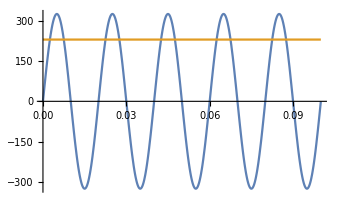

```mathematica
-Graphics-;

ClearAll["Global`*"]
frekvence = 50;
perioda = 1/frekvence;
tmax = 5*perioda;
Uef = 230;
amplituda = Uef*√2;
zasuvka = amplituda*Sin[2*π*frekvence*t];
Plot[{zasuvka, Uef},{t,0,tmax}]
```

```mathematica
(* PŘÍKLAD 6 *)
(* Můžeme do elektrické zásuvky s maximálním povoleným proudem 16 A připojit elektrickou troubu,která v turbo režimu má příkon 3,6 kW?Napětí v zásuvce je 230 V. *)

ClearAll["Global`*"]
Izmax = 16;
Uef = 230;
Ptrouba = 3.6*10^3;

Pz = Uef*Izmax
Pz>Ptrouba
```

3680

True

```mathematica
(* PŘÍKLAD 7*)
(*Rychlovarná konvice není nic jiného nežli výkonový rezistor.Konvice má na svém štítku údaj o tom,že při napětí Ueff=220 V má tepelný výkon 1850 W.Jak velký je proud,který teče konvicí?Jaký odpor má konvice?Jak se změní výkon konvice,pokud se napětí v zásuvce zvýší na Ueff=240 V?Na jakou hodnotu přitom vzroste proud,který teče konvicí (na alespoň takovýto proud musí být zásuvka dimenzována).*)
```

```mathematica
ClearAll["Global`*"]
UefCR = 220.;
Pkonvice = 1850;
Ikonvice = Pkonvice/UefCR
Rkonvice = UefCR/Ikonvice
UefF = 240.;
(* P = U*I == U^2/R== U*U/R *)
PkonviceF =UefF^2/Rkonvice
IkonviceF = PkonviceF/UefF
```

8.40909

26.1622

2201.65

9.17355

```mathematica
(* PŘÍKLAD 8 *)
(* Také elektrická plotýnka sporáku není nic jiného nežli výkonový rezistor.Plotýnka má jmenovitý výkon 600 W (jmenovitý výkon je výkon při jmenovitém napětí v elektrické síti,což je v našich končinách 230 V).Jak velký odpor má plotýnka?Jak velký proud teče plotýnkou při jmenovitém napětí?Napětí v síti může kolísat mezi 220 V a 240 V.Určete,jak může kolísat výkon plotýnky.Určete,jak může kolísat proud plotýnkou.V jakém rozmezí bude kolísat amplituda napětí? *)
```

```mathematica
ClearAll["Global`*"]
Pplotynka = 600.;
Uef = 230.;


Rplotynka = Uef^2/Pplotynka
Iplotynka = Pplotynka/Uef
Rplotynka1 = Uef/Iplotynka

Ukolisani ={220.,240.}
Pkolisani = Ukolisani^2/Rplotynka
Iplotynka = Pplotynka/Ukolisani

amplituda = √2*Ukolisani
```

88.1667

2.6087

88.1667

{220.,240.}

{548.96,653.308}

{2.72727,2.5}

{311.127,339.411}